Last modified on: Tuesday, July 19, 2022 at 18:22

Author Info

Peter Cullen Burbery

Connor Gray

Marshall University

https://community.wolfram.com/groups/-/m/t/2574372

Poster Session Content

Solving the Mixed Chinese Postman Problem

Solve the Mixed Chinese Postman Problem by implementing graph theory algorithms that are based on linear optimization in Mathematica.

In the below cell, please add the most representative image of your project here. (We recommend only one image, if you add more, we will make a collage of the images.)

-Graphics-

I was not able to create an algorithm that can find an optimal solution to the mixed Chinese postman problem but I was able to build a paclet with mixed graph functionality and submit it and update it in the Paclet Repository.

I hope to solve the Mixed Chinese Postman Problem in Mathematica and learn more about arc routing and combinatorial optimization. I would also like to apply it to real world data like ArcGIS and RouteSmart for mail delivery for example.

Note: Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more content."Add Header""Add Text""Add Code or Image"

The mixed Chinese Postman Problem MCPP is to find the minimal cost tour that crosses each edge and arc in a mixed graph at least once.

Code Example

Needs["PeterBurbery`MixedGraphs`"]
RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68,RandomInteger[{1,7}]&]

FindPostmanTour::ngen: The generalized FindPostmanTour[Graph[<54>, <156>]] is not implemented.

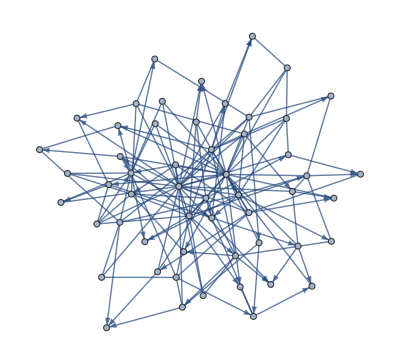
FindPostmanTour[-Graphics-]

This function generates a random mixed graphs with weights.

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"